```mathematica
IEEE 14 topology 
Graph[{1<->2,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5,4<->7,4<->9,5<->6,6<->11,6<->12,6<->13,7<->8,7<->9,9<->10,9<->14,10<->11,12<->13,13<->14},
VertexLabels->{1->Placed[{1,Slack},{Center,Above}],2->Placed[{2},{Center}],3->Placed[{3},{Center}],
4->Placed[{4},{Center}],5->Placed[{5},{Center}],6->Placed[{6},{Center}],7->Placed[{7},{Center}],8->Placed[{8},{Center}],9->Placed[{9},{Center}],10->Placed[{10},{Center}],
11->Placed[{11},{Center}],12->Placed[{12},{Center}],
13->Placed[{13},{Center}],Placed[{14},{Center}]},VertexSize->0.6,
VertexStyle->{1|2|9|13|6|0|3|4|5|7|8|10|11|12|14->White},
VertexShapeFunction->{2-> "Square",13-> "Square",6-> "Triangle",9-> "Triangle"},
EdgeStyle->{3<->4|10<->11|9<->10|12<->13|4<->7|5<->6->Black,Thickness[0.01],1<->5|2<->3|4<->5|1<->2|2<->5|2<->4|4<->9|6<->11|6<->12|6<->13|7<->8|7<->9|9<->14|13<->14->{Black,Dashed,Thick}},GraphLayout->"LayeredDrawing"]
```

```mathematica
(*
14 bus network.
1 slack
stochastic da spostare, da cambiare diverse cose
2 13 stocastici
6 9 controlalble deterministic
altri deterministici
RENUMERO I NODI
*)

Edges=20
Nodes=14
StochNodes=2;
(*DEFINITION OF EDGES-VERTEX MATRIX A-------------------------------*)
Amat=Table[0,{Edges},{Nodes}];
(*index 1 gives the entries of matrix A which must be set to 1. First component ranges form 1 to 20 edges), secondo component ranges from 1 to 13 (nodes) and it is the sending node for that edge*)
index1=  {  { 1,1},{2,1},
		{3,2},{4,2},{5,2},
                  {6,3},{7,3},{8,3},
		{9,4},
		{10,5},{11,5},{12,5},
		{13,6},
		{14,7},{15,7},
		{16,8},{17,8},
		{18,10},{19,10},
		{20,11}
                };
(*index 2 gives the entries of matrix A which must be set to -1. First component ranges form 1 to 20 edges), secondo component ranges from 1 to 13 (nodes) and it is the receiving node for that edge*)

index2=  {  {1,2},{2,6},
		{3,4},{4,5},{5,6},
                  {6,7},{7,13},{8,14},
		{9,5},
		{10,6},{11,8},{12,10},
		{13,7},
		{14,12},{15,13},
		{16,9},
		{17,10},
		{18,11},{19,14},
		{20,12}
                };

Amat=ReplacePart[Amat,index1->1];
Amat=ReplacePart[Amat,index2->-1];

(*DEFINITION OF DIAGONAL MATRIX D: for now all beta_[ij} are equal to 1*)

(*DEFINITION OF beta_{i,j}--------------------------------*)
(* index3 gives the pair of nodes which constitute an edge *)
index3=  {{1,2},{1,6},
		{2,4},{2,5},{2,6},
                  {3,7},{3,13},{3,14},
		{4,5},
		{5,6},{5,8},{5,10},
		{6,7},
		{7,12},{7,13},
		{8,9},{8,10},
		{10,11},{10,14},
		{11,12}
                };

(*CAMBIATO I DATI, CAMBIARE IL RESTO*)
(*************************************)
(*Actual betas*)
Betamat2={15.2631,
4.2350,
4.7819,
5.1158,
5.1939,
(*ora metto quelli che partono da 13*)
6.1028,
2.2520,
2.3150,
(*ora rimetto gli altri*)
5.0688,
21.5786,
4.7819,
1.7980,
3.9679,
4.0941,
3.1760,
5.6770,
9.0901,
10.3654,
3.0291,
4.4029};


(*Dmat=IdentityMatrix[Edges];*)
Dmat=DiagonalMatrix[Betamat2];
count=1;
Betamat=Table[0,{Nodes},{Nodes}];



For[i=1,i≤Nodes-1,i++,
For[j=1,j≤Nodes,j++,

If  [count≤20&&{i,j}==index3[[count]],
(Betamat[[i,j]]=Betamat2[[count]];
count=count+1),
(Unevaluated[Sequence[]] )
]
]
]



Betamat=Betamat+Transpose[Betamat];
MatrixForm[Betamat2];

(*Construction of admittance matrix B---------------------*)
Bmat=Table[0,{Nodes},{Nodes}];
Sumbeta=Table[0,{Nodes}];
For[i=1,i≤Nodes,i++,
For[k=1,k≤Nodes,k++,

   If[k≠ i,{Sumbeta[[i]]+=Betamat[[i,k]]},Sumbeta[[i]]=Sumbeta[[i]]];
] 
For[j=1,j≤Nodes,j++,
Bmat[[i,j]]=If[i≠j,-Betamat[[i,j]],Sumbeta[[i]]];
]
]

(*Construction of B hat*)
Btriang=Bmat[[2;;Nodes,2;;Nodes]];
Btrianginv=Inverse[Btriang];
"problema"
Bhat=ArrayFlatten[{{0,0},{0,Btrianginv}}];
(* Matrix check and visualization*)
(* COnstruction of matrices C,C_D, C^+ * 2 NODI STOCASTICI, FORSE DA CAMBIARE*)
Ctilde=Dmat.Amat.Bhat;
Cmat=Ctilde[[1;;Edges,2;;3]];
CDmat=Ctilde[[1;;Edges,4;;14]];
(* I_max sono uguali a 1 per ora*)
Cplus=Inverse[Transpose[Cmat].Cmat].Transpose[Cmat];
Checkmat=Cplus.Cmat;

 

(* \mu e \nu*)
(* power injections deterministiche da nodo 4 a nodo 14 / da 3 a 13 nel paper*)

mudet={-94.2,
         -47.8,
             -7.6,
	   -11.2,
	    0,
	   0,
	-29.5,
	-9,
	-3.5,
	-6.1,
	-14.9
}



(* funzioni segno e minimo *)
S[x_]:=Piecewise[{{1,0≤x}},-1];

(* dddddddddddddd*)

Lsquared=10*IdentityMatrix[2];
(*I_{max,l}=multiplo di vvinit[l]
calcolo vinit e poi modifico le matrici, cos= da ottenre quelle normalizzate. Se hocannato qualcosa bassta togliere le prossime tre 
righe e tutto torna come prima*)
CCmat=Drop[Cmat,{16}];
CCDmat=Drop[CDmat,{16}];
vinit=CCmat.{18.3,-13.5}+CCDmat.mudet;
alpha=1.5
"vinit"
vinit
CCmat=CCmat/(alpha*vinit);
CCDmat=CCDmat/(alpha*vinit);

v[x_,y_]:=CCmat.{18.3,-13.5}+CCDmat.{-94.2,-47.8,-7.6,x,0,0,y,-9,-3.5,-6.1,-14.9};
"v priam di togliere"
v[0,0]
vv[x_,y_]:=v[x,y];
(*v[x_,y_]:=Cmat.{18.3,-94.2}+CDmat.{x,y,-11.2,0,0,-29.5,-9,-3.5,-6.1,-13.5,-14.9}; vettore con tutte e venti le linee.
in realta' la linea 14 non dipende da x e y, e' costante. nel calcolo del current rate qindi 
dovrei dividere per zero, quindi la tolgo dalle linee interessanti*)


(*FIN QUI DOVREBE ESSERE GIUSTO*)
"MOMENTO VERITA'"
vv[ -11.2,-29.5]



(*AL MOMENTO CONTROLLO LEDUE STOCASTICHE*)
(*FARE CHECK CHE TUTE LE COMPONENTI DI V SIANO DIPENDENTI DA ALMENO UNO FRA x o y
vv[x_,y_]:=Delete[v[x,y],16] *)


prod1=Lsquared.Transpose[CCmat];
pprod1=Lsquared.Transpose[CCmat];
prod2=CCmat.prod1;

prodvec=Diagonal[prod2];
pprodvec=prodvec;
Denomin=DiagonalMatrix[prodvec];
DDenomin=Denomin; (*tolgo la linea nulla*)
"DDenomin"


DDenomininv=Inverse[DDenomin];


psi[x_,y_]:=DDenomininv.((Map[S,vv[x,y]]-vv[x,y])^2)

Minimo[x_,y_]:=Min[psi[x,y]];

(*psi,v,Denominv e' con 14 rimossa*)


P[x_,y_]:=(Max[Map[Abs,vv[x,y]]]<1);
Pall[x_,y_]:=(Max[Map[Abs,v[x,y]]]<1);
pos[x_,y_]:=First[Position[psi[x,y],Minimo[x,y]]];

"R"
R[x_,y_]:=CCmat.(pprod1[[All,pos[x,y][[1]]]])(1/pprodvec[[pos[x,y][[1]]]]);

(*pprod1 e' L^2*(2x19)
pprodvec e' lungo 19*)
(*R[x_,y_]:=Cmat.(prod1[[All,pos[x,y][[1]]]])(1/prodvec[[pos[x,y][[1]]]]);*)
(************************************************************************************************ARRIVATO QUI*)
```

20

14

problema

{-94.2,-47.8,-7.6,-11.2,0,0,-29.5,-9,-3.5,-6.1,-14.9}

1.5

vinit

{146.28,72.7196,71.5297,53.6437,39.407,-17.1732,-1.17712,4.85031,-22.6703,-62.5502,29.053,16.6706,41.9764,6.32613,7.27712,29.053,6.17387,10.0497,-2.82613}

v priam di togliere

{0.548592,0.531059,0.616471,0.527509,0.508913,0.61187,0.494057,0.430761,0.825044,0.576182,0.301094,0.301094,0.418479,0.381,0.638746,0.301094,0.959378,0.780523,0.0272186}

MOMENTO VERITA'

{0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667}

DDenomin

R

0.5

1

1

0.25

1/10000000

C3

1.

lower bound

ciao

ciao

ciao

«1 more identical outputs»

conticini

2.

0.512019

1.02404

4.02952

1.

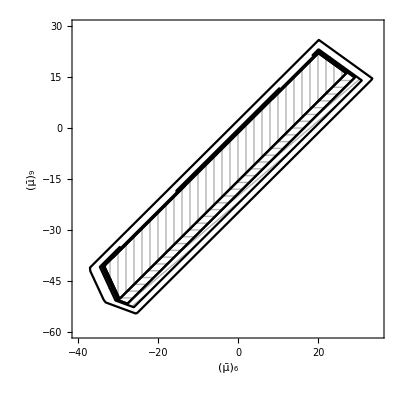

```mathematica
(*n,and K=1.5.We
set T=1,γi=1,li=10,.0f=0.25 and τ=0.5. *)

tau=0.5;
T=1;
gamma=1;
eps=0.25;
p=1/10000;

COST1[gamma_,T_]:=gamma/(1-Exp[-2gamma*T])
COST2[eps_,p_]:=eps*Log[1/p]
COST3[gamma_,tau_]:=2*gamma*tau
COST4[gamma_,tau_]:=1-Exp[-gamma*T]
C1=COST1[gamma,T];
C2=COST2[eps,p];
C3=COST3[gamma,tau]
C4=COST4[gamma,tau];

alphaa[x_,y_]:=Sqrt[(1-vv[x,y]^2*Exp[-T/tau])/(1-Exp[-T/tau])];
Lowerbound[x_,y_]:=MapThread[Min,{(gamma*(alphaa[x,y]-vv[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T])),
                                                       (gamma*(-alphaa[x,y]-vv[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T]))}];
ICURRENT[x_,y_]:=C1*Minimo[x,y];
ITAYLORmod3[x_,y_]:=ICURRENT[x,y]*(1+C3);



Show[RegionPlot[P[x,y],{x,-40,35},{y,-60,30},MaxRecursion->4,PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ICURRENT[x,y]≥C2,{x,-40,35},{y,-60,30},MaxRecursion->4,MeshFunctions->{#1&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12}FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&Min[Lowerbound[x,y]]≥C2&&ICURRENT[x,y]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ITAYLORmod3[x,y]≥C2&&Min[Lowerbound[x,y]]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#1-#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}]
]
```

```mathematica
(* bettere figures with polygons *)
```

Polygon[{{0,0},{0,0}}]

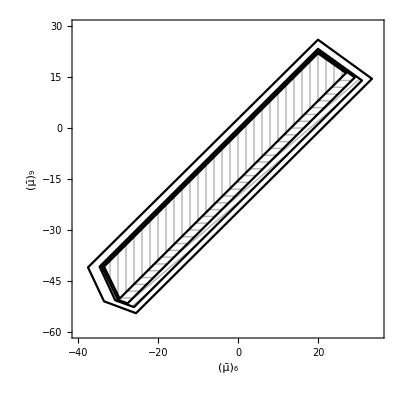

```mathematica
P0=Polygon[{{0,0},{0,0}}]
P1=Polygon[{{20,26},{33.5,14.5},{-25.5,-54.5},{-33.5,-51},{-37.5,-41}}];
Ptaylor=Polygon[{{20,23.3},{31,14},{-26,-52.7},{-30.7,-50.7},{-34.6,-40.8}}];
Plb=Polygon[{{20,22.6},{29.2,14.9},{-27.6,-51.6},{-30,-50.6},{-34,-40.9}}];
Pcurrent=Polygon[{{20,22},{27,16.2},{-29.6,-50.2},{-33.5,-40.8}}];


h0=RegionPlot[{P0==0},{x,-40,35},{y,-60,30},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
h1=RegionPlot[P1,BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
htaylor=RegionPlot[Ptaylor,MeshFunctions->{#1-#2&},Mesh->{Range[-60,50,2]},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
hlb=RegionPlot[Plb,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
hcurrent=RegionPlot[Pcurrent,MeshFunctions->{#1&},Mesh->{Range[-60,50,2]},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
Show[h0,h1,htaylor,hlb,hcurrent]
```

1.

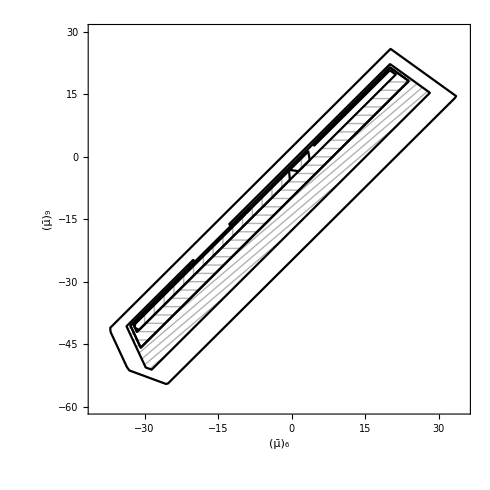

```mathematica
tau=0.5;
T=1;
gamma=1;
eps=0.25;
p=1/10000000;

COST1[gamma_,T_]:=gamma/(1-Exp[-2gamma*T])
COST2[eps_,p_]:=eps*Log[1/p]
COST3[gamma_,tau_]:=2*gamma*tau
COST4[gamma_,tau_]:=1-Exp[-gamma*T]
C1=COST1[gamma,T];
C2=COST2[eps,p];
C3=COST3[gamma,tau]
C4=COST4[gamma,tau];

alphaa[x_,y_]:=Sqrt[(1-vv[x,y]^2*Exp[-T/tau])/(1-Exp[-T/tau])];
Lowerbound[x_,y_]:=MapThread[Min,{(gamma*(alphaa[x,y]-vv[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T])),
                                                       (gamma*(-alphaa[x,y]-vv[x,y])^2)/(pprodvec*(1-Exp[-2*gamma*T]))}];
ICURRENT[x_,y_]:=C1*Minimo[x,y];
ITAYLORmod3[x_,y_]:=ICURRENT[x,y]*(1+C3);



Show[RegionPlot[P[x,y],{x,-40,35},{y,-60,30},MaxRecursion->4,PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ICURRENT[x,y]≥C2,{x,-40,35},{y,-60,30},MaxRecursion->4,MeshFunctions->{#1&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12}FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&Min[Lowerbound[x,y]]≥C2&&ICURRENT[x,y]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}],

RegionPlot[P[x,y]&&ITAYLORmod3[x,y]≥C2&&Min[Lowerbound[x,y]]<=C2,{x,-40,35},{y,-60,30},MaxRecursion->4,PlotPoints->80,MeshFunctions->{#1-#2&},Mesh->{Range[-60,50,2]},PlotStyle->None,BoundaryStyle->Black,BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}]
]
```

```mathematica
(* Better pictures using polygons *)
```

Polygon[{{0,0},{0,0}}]

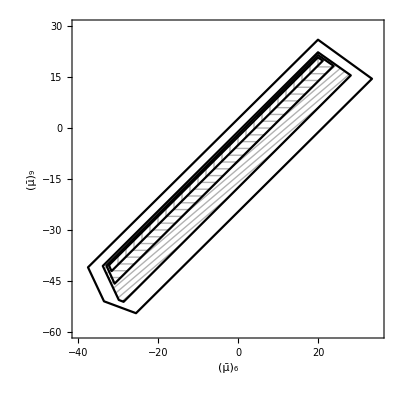

```mathematica
P0=Polygon[{{0,0},{0,0}}]
P1=Polygon[{{20,26},{33.5,14.5},{-25.5,-54.5},{-33.5,-51},{-37.5,-41}}];
Ptaylor=Polygon[{{20,22.3},{28.2,15.5},{-28.6,-51.15},{-29.8,-50.6},{-33.8,-40.6}}];
Plb=Polygon[{{20,21.5},{23.9,18.3},{-30.85,-45.8},{-32.9,-40.5}}];
Pcurrent=Polygon[{{20,20.8},{21.2,19.8},{-31.6,-42.1},{-32.3,-40.4}}];

h0=RegionPlot[{P0==0},{x,-40,35},{y,-60,30},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
h1=RegionPlot[P1,BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
htaylor=RegionPlot[Ptaylor,MeshFunctions->{#1-#2&},Mesh->{Range[-60,50,2]},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
hlb=RegionPlot[Plb,MeshFunctions->{#2&},Mesh->{Range[-60,50,2]},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
hcurrent=RegionPlot[Pcurrent,MeshFunctions->{#1&},Mesh->{Range[-60,50,2]},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
Show[h0,h1,htaylor,hlb,hcurrent]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

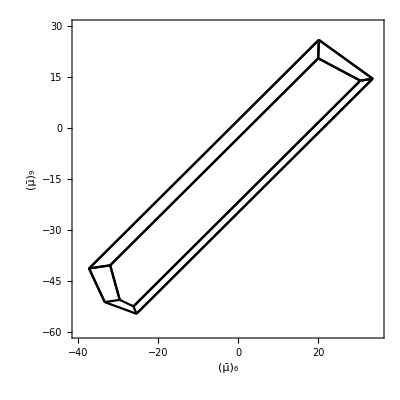

Polygon[{{0,0},{0,0}}]

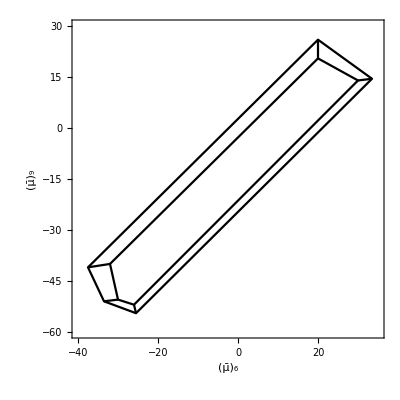

```mathematica
(* Manca la parte dove calcolo questa suddivision in regioni
 *)g00=RegionPlot[{P[x,y],
P[x,y]&&pos[x,y][[1]]==9,
P[x,y]&&pos[x,y][[1]]==11,
P[x,y]&&pos[x,y][[1]]==13,
P[x,y]&&pos[x,y][[1]]==17,
P[x,y]&&pos[x,y][[1]]==19,
P[x,y]&&pos[x,y][[1]]==7
(*P[x,y]&&ICURRENT[x,y]≥C2&&pos[x,y][[1]]==7
P[x,y]&&psi[x,y][[2]]<=ICURRENT[x,y],
P[x,y]&&psi[x,y][[3]]<=ICURRENT[x,y],
P[x,y]&&psi[x,y][[4]]<=ICURRENT[x,y]*)
                   },{x,-40,35},{y,-60,30},PlotStyle->White,BoundaryStyle->Black,PlotPoints->50,MaxRecursion->4,
BaseStyle->{FontFamily->"Times",FontSize->12},FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}]
(* PlotLegends->{"Initial region","(3,4)","(4,7)","(5,6)","(9,10)","(10,11)","(12,13)"}]*)



P0=Polygon[{{0,0},{0,0}}]
P1=Polygon[{{20,26},{33.5,14.5},{-25.5,-54.5},{-33.5,-51},{-37.5,-41}}];
P2b=Polygon[{{20,20.5},{30,14},{-26,-52},{-30,-50.5},{-32,-40}}];
P3b=Line[{{{20,26},{20,20.5}},{{33.5,14.5},{30,14}},
       {{-25.5,-54.5},{-26,-52}},{{-33.5,-51},{-30,-50.5}},{{-37.5,-41},{-32,-40}}}];

g0=RegionPlot[{P0==0},{x,-40,35},{y,-60,30},BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
g1=RegionPlot[P1,BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];

g2=RegionPlot[P2b,BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
g3=RegionPlot[P3b,BaseStyle->{FontFamily->"Times",FontSize->12},PlotStyle->White,BoundaryStyle->Black,
FrameLabel->{Style[Subscript[OverBar[μ], 6],FontFamily->"Times New Roman",FontSize->14],Style[Subscript[OverBar[μ], 9],FontFamily->"Times New Roman",FontSize->14]}];
Show[g0,g1,g2,g3]
```